```mathematica
Integrate[x^2,{x,0,1}]
```

1/3

```mathematica
Integrate[x^2*1/x,{x,0,1}]
```

1/2

```mathematica
2*Integrate[x*(1-x)*1/x,{x,0,1}]
```

1

```mathematica
-x*D[x^2,x]+1/2*x*(1-x)*D[x^2,{x,2}]//FullSimplify
```

x-3 x^2

```mathematica
-x*D[x*(1-x),x]+1/2*x*(1-x)*D[x*(1-x),{x,2}]
```

-(1-2 x) x-(1-x) x

```mathematica
DSolve[{D[f[t],t]==-f[t],f[0]==x0},f,t]
```

{{f→Function[{t},ⅇ^-t x0]}}

```mathematica
DSolve[{D[f[t],t]==x0*Exp[-t]-3*f[t],f[0]==x0^2},f,t]
```

{{f→Function[{t},1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)]}}

```mathematica
1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)//FullSimplify
```

```mathematica
pHom = 1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)
```

1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)

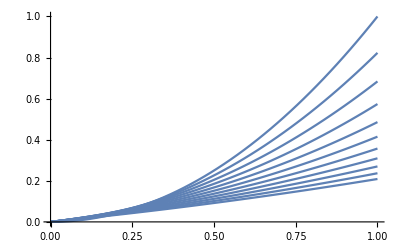

```mathematica
Plot[Table[1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0),{t,0,1,.1}],{x0,0,1}]
```

```mathematica
pHet = 2*(x0*Exp[-t]-pHom)//FullSimplify
```

ⅇ^(-3 t) (1+ⅇ^(2 t)-2 x0) x0

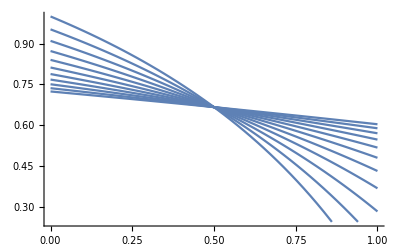

```mathematica
Plot[Table[pHet/(pHet+pHom),{t,0,1,.1}],{x0,0,1}]
```

```mathematica
pHetgHetHom = pHet/(pHet+pHom)//FullSimplify
```

1/(3/2+(-1+2 x0)/(1+ⅇ^(2 t)-2 x0))

```mathematica
pHetAncTable = Table[Table[pHetgHetHom,{x0,.01,.99,.01}],{t,0,1,.1}];
```

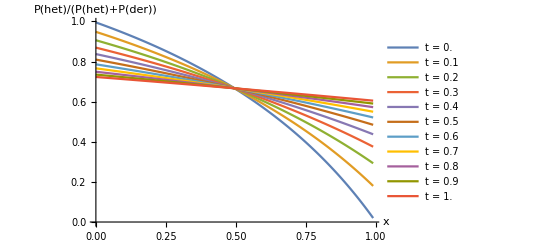

```mathematica
ListLinePlot[pHetAncTable,PlotRange->All,DataRange->{.0,.99},PlotLegends->Table[StringForm["t = ``",ti],{ti,0,1,.1}],AxesLabel->{"x","P(het)/(P(het)+P(der))"}]
```

```mathematica
pHetgHetHom/.{t->.01,x0->.01}
```

0.990051

```mathematica
ExAnc = ⅇ^-t x0/.t->t1
```

ⅇ^-t1 x0

```mathematica
Ex2Anc = 1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)/.t->t1
```

1/2 ⅇ^(-3 t1) x0 (-1+ⅇ^(2 t1)+2 x0)

```mathematica
ExSplit = x0*Exp[-t1]
```

ⅇ^-t1 x0

```mathematica
Ex2Split = (Exp[-t1]-1/2*Exp[-(3*t1+t2)]-1/2*Exp[-(t1+t2)])*x0+Exp[-(3*t1+t2)]*x0^2
```

(ⅇ^-t1-1/2 ⅇ^(-3 t1-t2)-ⅇ^(-t1-t2)/2) x0+ⅇ^(-3 t1-t2) x0^2

```mathematica
pHetgHetHomSplit = 1-Ex2Split/(2*ExSplit-Ex2Split)//FullSimplify
```

1/(1/2+ⅇ^(2 t1+t2)/(1+ⅇ^(2 t1)-2 x0))

```mathematica
pHetgHetHomAnc = 1-Ex2Anc/(2*ExAnc-Ex2Anc)//FullSimplify
```

1/(3/2+(-1+2 x0)/(1+ⅇ^(2 t1)-2 x0))

```mathematica
pHetSplitTable = Table[Table[pHetgHetHomSplit/.t2->t1-.1,{x0,.01,.99,.01}],{t1,.1,1,.1}];
```

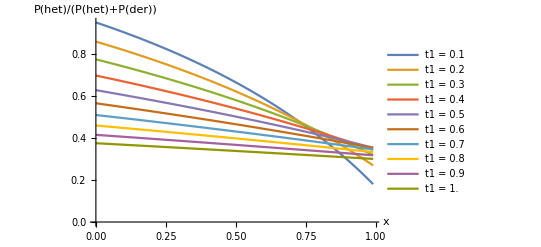

```mathematica
ListLinePlot[pHetSplitTable,PlotRange->All,DataRange->{.0,.99},PlotLegends->Table[StringForm["t1 = ``",ti],{ti,.1,1,.1}],AxesLabel->{"x","P(het)/(P(het)+P(der))"}]
```

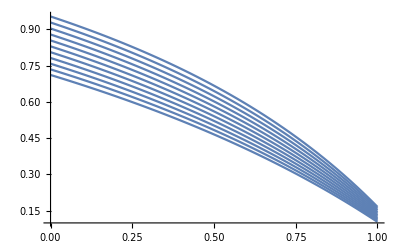

```mathematica
Plot[Table[pHetgHetHomSplit/.t1->0.1,{t2,0,.5,.05}],{x0,0,1}]
```

```mathematica
blah = pHetgHetHomAnc/pHetgHetHomSplit//FullSimplify
```

(1+ⅇ^(2 t1) (1+2 ⅇ^t2)-2 x0)/(1+3 ⅇ^(2 t1)-2 x0)

```mathematica
3*(3-1)/2
```

3

```mathematica
Q = {{0,0,0},{1,-1,0},{0,3,-3}}
```

```mathematica
{{0,0,0},{1,-1,0},{0,3,-3}}//MatrixForm
```

(0 | 0 | 0
1 | -1 | 0
0 | 3 | -3)

```mathematica
MatrixExp[Q*t].{x,x^2,x^3}//FullSimplify
```

{x,x+ⅇ^-t (-1+x) x,1/2 x (2+ⅇ^(-3 t) (-1+x) (-1+3 ⅇ^(2 t)+2 x))}

```mathematica
-3*(3+1)/2
```

-6

```mathematica
Qd = {{-1,0,0},{1,-3,0},{0,3,-6}}
```

{{-1,0,0},{1,-3,0},{0,3,-6}}

```mathematica
Truth = MatrixExp[Q*t2].MatrixExp[Qd*t1].{x,x^2,x^3}
```

{ⅇ^-t1 x,(1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2)) x+ⅇ^(-3 t1-t2) x^2,(1/10 ⅇ^(-6 t1-3 t2) (-1+ⅇ^t1)^2 (2+4 ⅇ^t1+6 ⅇ^(2 t1)+3 ⅇ^(3 t1))+1/2 ⅇ^(-t1-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2)+3/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2))) x+(ⅇ^(-6 t1-3 t2) (-1+ⅇ^(3 t1))+3/2 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t2))) x^2+ⅇ^(-6 t1-3 t2) x^3}

```mathematica
(Ex2Split/.x0->x)/((1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2)) x+ⅇ^(-3 t1-t2) x^2)//FullSimplify
```

1

```mathematica
blah  = MatrixExp[Q*t2].MatrixExp[Qd*t1]
```

{{ⅇ^-t1,0,0},{1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2),ⅇ^(-3 t1-t2),0},{1/10 ⅇ^(-6 t1-3 t2) (-1+ⅇ^t1)^2 (2+4 ⅇ^t1+6 ⅇ^(2 t1)+3 ⅇ^(3 t1))+1/2 ⅇ^(-t1-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2)+3/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2)),ⅇ^(-6 t1-3 t2) (-1+ⅇ^(3 t1))+3/2 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t2)),ⅇ^(-6 t1-3 t2)}}

```mathematica
Truth2 = blah.{x,x^2,x^3}
```

{ⅇ^-t1 x,(1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2)) x+ⅇ^(-3 t1-t2) x^2,(1/10 ⅇ^(-6 t1-3 t2) (-1+ⅇ^t1)^2 (2+4 ⅇ^t1+6 ⅇ^(2 t1)+3 ⅇ^(3 t1))+1/2 ⅇ^(-t1-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2)+3/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2))) x+(ⅇ^(-6 t1-3 t2) (-1+ⅇ^(3 t1))+3/2 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t2))) x^2+ⅇ^(-6 t1-3 t2) x^3}

```mathematica
Truth3 = blah.Table[Beta[k-1/2+i,n-k-1/2]/Beta[k-1/2,n-k-1/2],{i,1,3}]//FullSimplify
```

{(ⅇ^-t1 (-1+2 k))/(2 (-1+n)),(ⅇ^(-3 t1-t2) (-1+2 k) (1+2 k+(-1+ⅇ^(2 t1) (-1+2 ⅇ^t2)) n))/(4 (-1+n) n),(ⅇ^(-3 (2 t1+t2)) (-1+2 k) (4+ⅇ^(3 t1) (5+ⅇ^(2 t1)+20 ⅇ^(2 t1+3 t2)-15 ⅇ^(2 t2) (1+ⅇ^(2 t1)))+(5 (-2+ⅇ^(3 t1) (-1+3 ⅇ^(2 t2))) (1+2 k))/n+(5 (3+4 k (2+k)))/(n (1+n))))/(40 (-1+n))}

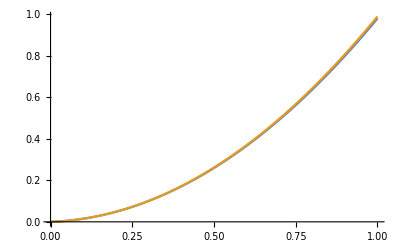

```mathematica
Plot[{Truth[[2]]/.{t1->.01,t2->.05},Truth3[[2]]/.k->x*n/.{n->100,t1->.01,t2->.05}},{x,0,1}]
```

```mathematica
FullSimplify[Beta[k+m,n-k+1]/Beta[k,n-k+1],Assumptions->Element[k,Integers]&&Element[n,Integers]&&Element[m,Integers]&&k>0&&m>0&&n>0]
```

(n! Gamma[k+m])/((m+n)! Gamma[k])

```mathematica
Integrate[x^m*x^(k-1)*(1-x)^(n-k),{x,0,1}]
```

ConditionalExpression[(Gamma[k+m] Gamma[1-k+n])/Gamma[1+m+n],Re[k-n]<1&&Re[k+m]>0]